Model

```mathematica
Subscript[f, R]=x (1 - x)-(Subscript[a, 1] x y)/(1+Subscript[b, 1] x);
Subscript[f, C]=(Subscript[a, 1] x y)/(1+Subscript[b, 1] x)-(Subscript[a, 2] y z)/(1+Subscript[b, 2] y)-Subscript[d, 1] y;
Subscript[f, P]=(Subscript[a, 2] y z)/(1+Subscript[b, 2] y)-Subscript[d, 2] z;
```

```mathematica
param ={
Subscript[a, 1]->5.0,
Subscript[a, 2]->0.1,
Subscript[b, 2]->2.0,
Subscript[d, 1]->0.4,
Subscript[d, 2]->0.01
};
```

Attractor Structure

```mathematica
subs = Join[param,{x->x[t],y->y[t],z->z[t]}];
model={x'[t]==(Subscript[f, R]/.subs),y'[t]==(Subscript[f, C]/.subs),z'[t]==(Subscript[f, P]/.subs)};
sol=NDSolve[Join[model,{x[0]==0.8,y[0]==0.2,z[0]==10.0}]/.Subscript[b, 1]->3.0,{x,y,z},{t,10000},MaxSteps->50000];
solDiverge=NDSolve[Join[model,{x[0]==0.81,y[0]==0.21,z[0]==10.1}]/.Subscript[b, 1]->3.0,{x,y,z},{t,10000},MaxSteps->50000];
```

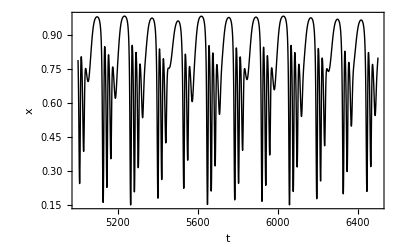

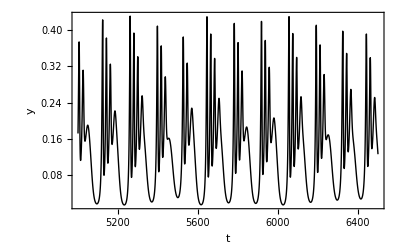

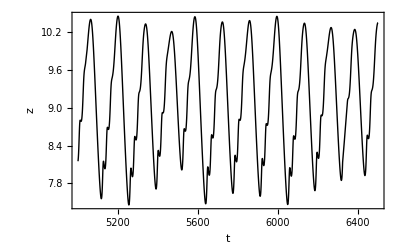

```mathematica
Plot[Evaluate[x[t]/.sol],{t,5000,6500},FrameLabel->{"t","x"},Frame->True,Axes->False,PlotRange->All,PlotStyle->Black]
Plot[Evaluate[y[t]/.sol],{t,5000,6500},FrameLabel->{"t","y"},Frame->True,Axes->False,PlotRange->All,PlotStyle->Black]
Plot[Evaluate[z[t]/.sol],{t,5000,6500},FrameLabel->{"t","z"},Frame->True,Axes->False,PlotRange->All,PlotStyle->Black]
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,5000,6400},PlotRange->{{0,1},{0,0.5},{7.5,10.5}},BoxRatios->{1,1,1},PlotStyle->Black,AspectRatio->1,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

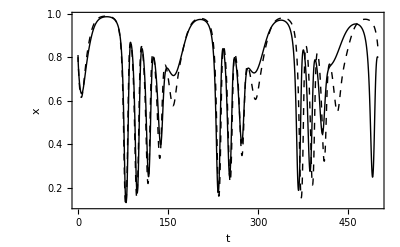

```mathematica
Plot[{Evaluate[{x[t]/.sol}],Evaluate[{x[t]/.solDiverge}]},{t,0,500},FrameLabel->{"t","x"},Frame->True,Axes->False,PlotStyle->{Black,{Black,Dashed}}]
```

Bifurcation Analysis

Letting the system approach the attractor for each value of b_1 used, we then plotted successive maxima of z as a function of b_1. We used values of b_1 between 2.0 and 3.2, changing b_1 in steps of 0.01, and values of b_1 from 3.2 to 6.2, changing b_1 in steps of 0.1. We did this both by starting with the smaller value of b_1 and increasing b_1 , and also by starting with the larger value of b_1 and decreasing b_1.

```mathematica
(* find the local maxima utility function *)
localMax=Compile[{{val,_Real,1}},
#[[2]]&/@Select[Partition[val,3,1],(#[[1]]<#[[2]]>#[[3]])||(#[[1]]==#[[2]]==#[[3]])&],
CompilationTarget->"C"
];
```

```mathematica
(* find the equilibrium values along the bifurcation parameter to give a good set of initial values *)
eqs[min_,max_,step_] :=Table[Solve[{Subscript[f, R]==0,Subscript[f, C]==0,Subscript[f, P]==0,x>0,y>0,z>0}/.param/.Subscript[b, 1]->b,{x,y,z}][[1]],{b,min,max,step}]/.{x->R,y->C,z->P};
```

```mathematica
Subscript[b, min]=2.2;
Subscript[b, max]=3.2;
step=0.001;
initVals={x[0]==R,y[0]==C,z[0]==0.98 P}/.eqs[Subscript[b, min],Subscript[b, max],step];
bs=Range[Subscript[b, min],Subscript[b, max],step];
bifTS=ParallelTable[NDSolve[Join[model,initVals[[i]]]/.Subscript[b, 1]->bs[[i]],{x,y,z},{t,10000},MaxSteps->50000],{i,Length[bs]}];//Timing
```

{3.08882,Null}

```mathematica
Dimensions[bifTS]
```

{1001,1,3}

{14.11809,Null}

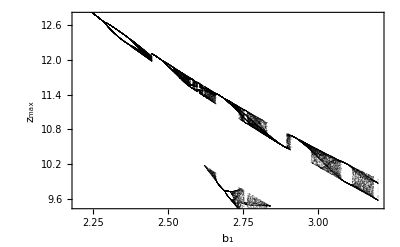

```mathematica
(* plot the result *)
vals=Flatten[z/.#&/@bifTS];
bif=Flatten[Table[{bs[[i]],#}&/@localMax[vals[[i]][Range[5000,10000]]],{i,1,Length[bs]}],1];//Timing
ListPlot[bif,FrameLabel->{"b_1","z_max"},Frame->True,Axes->False,PlotStyle->{PointSize[0.001],RGBColor[0,0,0,0.5]},PlotRange->{{2.2,3.2},{9.5,12.75}}]
```

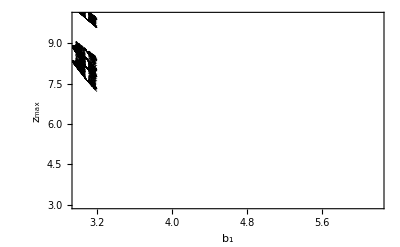

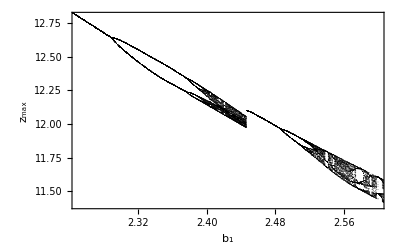

```mathematica
ListPlot[bif,FrameLabel->{"b_1","z_max"},Frame->True,Axes->False,PlotStyle->{PointSize[0.001],Black},PlotRange->{{3.0,6.2},{3,10}}]
ListPlot[bif,FrameLabel->{"b_1","z_max"},Frame->True,Axes->False,PlotStyle->{PointSize[0.001],Black},PlotRange->{{2.25,2.6},{11.4,12.8}}]
```